# Practical 7

Plotting the characteristics of the first order PDE

(y^2up/x)+ xup = y^2

```mathematica
a[u_,x_,y_]:=y[x]^2* u[x,y]/x
```

```mathematica
b[u_,x_,y_]:=u[x,y]x
```

```mathematica
sol=DSolve[y'[x]==b[u,x,y]/a[u,x,y],y[x],x]
```

{{y[x]→(x^3+3 C[1])^(1/3)},{y[x]→-(-1)^(1/3) (x^3+3 C[1])^(1/3)},{y[x]→(-1)^(2/3) (x^3+3 C[1])^(1/3)}}

```mathematica
tab1=Table[y[x]/.sol[[1,1]]/.C[1]->i,{i,-2,2}]
```

{(-6+x^3)^(1/3),(-3+x^3)^(1/3),(x^3)^(1/3),(3+x^3)^(1/3),(6+x^3)^(1/3)}

```mathematica
tab2=Table[y[x]/.sol[[2,1]]/.C[1]->i,{i,-2,2}]
```

{-(-1)^(1/3) (-6+x^3)^(1/3),-(-1)^(1/3) (-3+x^3)^(1/3),-(-1)^(1/3) (x^3)^(1/3),-(-1)^(1/3) (3+x^3)^(1/3),-(-1)^(1/3) (6+x^3)^(1/3)}

```mathematica
tab3=Table[y[x]/.sol[[3,1]]/.C[1]->i,{i,-2,2}]
```

{(-1)^(2/3) (-6+x^3)^(1/3),(-1)^(2/3) (-3+x^3)^(1/3),(-1)^(2/3) (x^3)^(1/3),(-1)^(2/3) (3+x^3)^(1/3),(-1)^(2/3) (6+x^3)^(1/3)}

```mathematica
Plot[{Evaluate[tab1],Evaluate[tab2],Evaluate[tab3]},{x,-5,5},PlotLegends->"Expressions"]
```

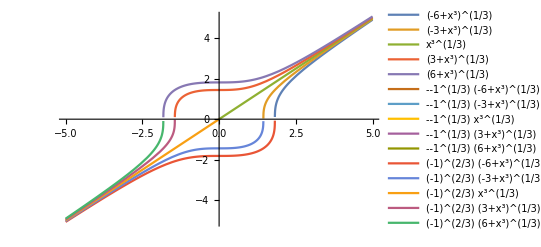

ptanx+qtany=tanz

```mathematica
a[u_,x_,y_]:=Tan[x]
```

```mathematica
b[u_,x_,y_]:=Tan[y[x]]
```

```mathematica
sol=DSolve[y'[x]==b[u,x,y]/a[u,x,y],y[x],x]
```

{{y[x]→ArcSin[1/2 C[1] Sin[x]]}}

```mathematica
tab1=Table[y[x]/.sol[[1,1]]/.C[1]->i,{i,-2,2}]
```

```mathematica
Plot[{Evaluate[tab1]},{x,-5,5},PlotLegends->"Expressions"]
```

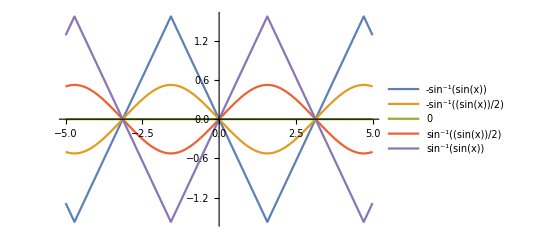

x(y^2-z^2)q-y(z^2+x^2)q=z(x^2+y^2)

```mathematica
a[u_,x_,y_]:=x^2
```

```mathematica
b[u_,x_,y_]:=y[x]^2
```

```mathematica
sol=DSolve[y'[x]==b[u,x,y]/a[u,x,y],y[x],x]
```

{{y[x]→-x/(-1+x C[1])}}

```mathematica
tab1=Table[y[x]/.sol[[1,1]]/.C[1]->i,{i,-2,2}]
Plot[{Evaluate[tab1]},{x,-10,10},PlotLegends->"Expressions"]
```

{-x/(-1-2 x),-x/(-1-x),x,-x/(-1+x),-x/(-1+2 x)}

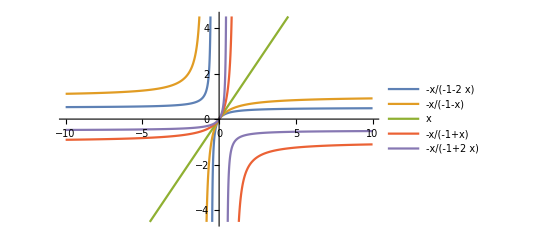

u_X - u_y = 1

```mathematica
a[u_,x_,y_]:=1
```

```mathematica
b[u_,x_,y_]:=-1
```

```mathematica
sol=DSolve[y'[x]==b[u,x,y]/a[u,x,y],y[x],x]
```

{{y[x]→-x+C[1]}}

```mathematica
tab1=Table[y[x]/.sol[[1,1]]/.C[1]->i,{i,-2,2}]
Plot[{Evaluate[tab1]},{x,-10,10},PlotLegends->"Expressions"]
```

{-2-x,-1-x,-x,1-x,2-x}

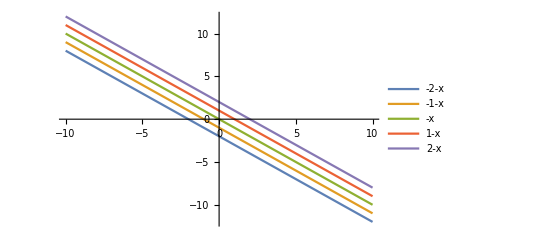

xu_x+ yu_y = u

```mathematica
a[x_,y_,u_]:=x
```

```mathematica
b[x_,y_,u_]:=y[x]
```

```mathematica
sol=DSolve[y'[x]==b[x,y,u]/a[x,y,u],y[x],x]
```

{{y[x]→x C[1]}}

```mathematica
tab=Table[y[x]/.sol/.C[1]->i,{i,-10,10}]//Flatten
```

{-10 x,-9 x,-8 x,-7 x,-6 x,-5 x,-4 x,-3 x,-2 x,-x,0,x,2 x,3 x,4 x,5 x,6 x,7 x,8 x,9 x,10 x}

```mathematica
Plot[Evaluate[tab],{x,-2,2},PlotLegends->"Expressions"]
```

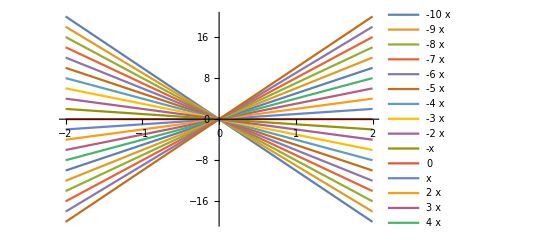

```mathematica
Clear[y,x,u,a,b,sol]
```

u(x+y)u_x + u(x-y)u_y = x^2 + y^2

```mathematica
a[u_,x_,y_]:=u[x,y](x+y[x])
```

```mathematica
b[u_,x_,y_]:=u[x,y](x-y[x])
```

```mathematica
sol=DSolve[y'[x]==b[u,x,y]/a[u,x,y],y[x],x]
```

{{y[x]→-x-√(ⅇ^(2 C[1])+2 x^2)},{y[x]→-x+√(ⅇ^(2 C[1])+2 x^2)}}

```mathematica
tab1=Table[y[x]/.sol[[1,1]]/.C[1]->i,{i,-2,2}]
```

{-x-√(1/ⅇ^4+2 x^2),-x-√(1/ⅇ^2+2 x^2),-x-√(1+2 x^2),-x-√(ⅇ^2+2 x^2),-x-√(ⅇ^4+2 x^2)}

```mathematica
tab2=Table[y[x]/.sol[[2,1]]/.C[1]->i,{i,-2,2}]
```

{-x+√(1/ⅇ^4+2 x^2),-x+√(1/ⅇ^2+2 x^2),-x+√(1+2 x^2),-x+√(ⅇ^2+2 x^2),-x+√(ⅇ^4+2 x^2)}

```mathematica
Plot[{Evaluate[tab1],Evaluate[tab2]},{x,-5,5},PlotLegends->"Expressions"]
```